```mathematica
f[x_]:=Log[x]
```

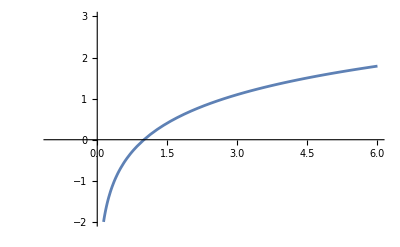

```mathematica
Plot[f[x],{x,-1,6},PlotRange->{{-1,6},{-2,3}}]
```

```mathematica
g[x_]:=x-1
```

```mathematica
h[x_]:=x/E
```

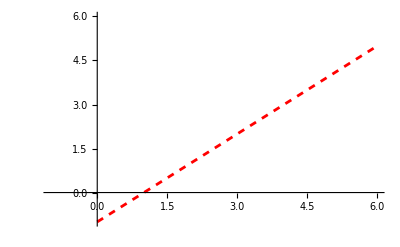

```mathematica
Plot[g[x], {x, -1, 6}, PlotRange -> {-1,6}, PlotStyle -> {Red, Dashed}]
```

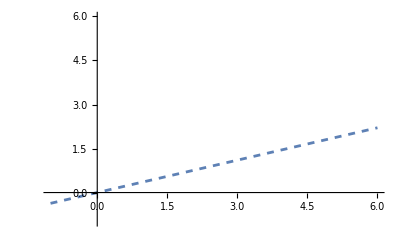

```mathematica
Plot[h[x], {x,-1,6}, PlotRange -> {-1,6}, PlotStyle -> {Grey, Dashed}]
```

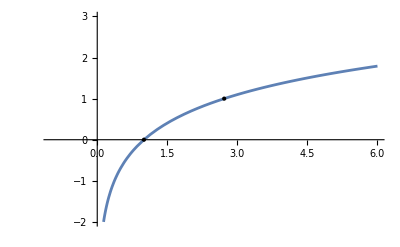

```mathematica
Show[Plot[f[x],{x,-1,6},PlotRange->{{-1,6},{-2,3}}],Graphics[{PointSize[Large],Point[{1,0}],Point[{E,Log[E]}]}]]
```

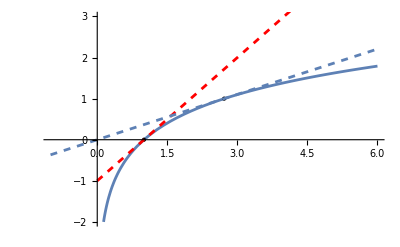

```mathematica
Show[Plot[f[x],{x,-1,6},PlotRange->{{-1,6},{-2,3}}],Graphics[{PointSize[Large],Point[{1,0}],Point[{E,Log[E]}]}],Plot[g[x],{x,-1,6},PlotRange->{-1,6},PlotStyle->{Red,Dashed}],Plot[h[x],{x,-1,6},PlotRange->{-1,6},PlotStyle->{Grey,Dashed}]]
```

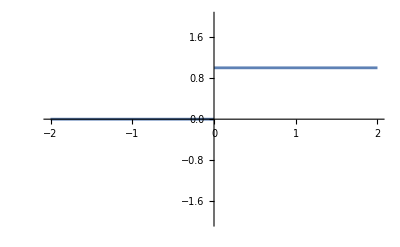

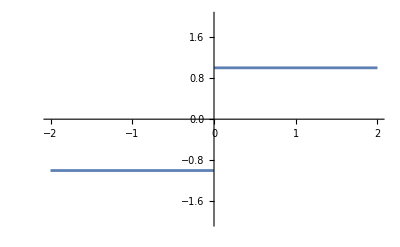

```mathematica
H[x_]:=Piecewise[{{0,x<0},{1,x>=0}}]
G[x_]:=2*H[x]-1
Plot[H[x], {x,-2,2}, PlotRange->{{-2,2},{-2,2}}]
Plot[G[x],{x,-2,2},PlotRange->{{-2,2},{-2,2}}]
```

```mathematica
Int1[x_] =Integrate[G[x],x]
```

Piecewise[{{-x, x≤0}, {x, True}}]

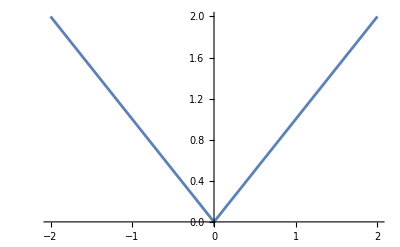

```mathematica
Plot[Piecewise[{{-x,x<=0}},x],{x,-2,2}]
```

```mathematica
Int2[x_] = Integrate[Int1[x],x]
```

Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]

```mathematica
Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]
```

Piecewise[{{-x^2/2, x≤0}, {x^2/2, True}}]

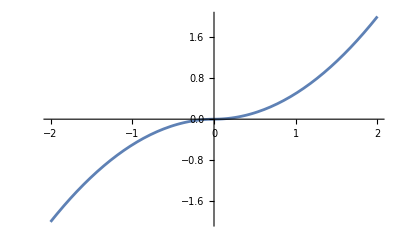

```mathematica
Plot[Piecewise[{{-(x^2/2),x<=0}},x^2/2],{x,-2,2}]
```

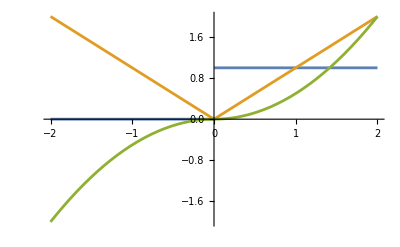

```mathematica
Plot[{Piecewise[{{0,x<0},{1,x>=0}}],Piecewise[{{-x,x<=0}},x],Piecewise[{{-(x^2/2),x<=0}},x^2/2]},{x,-2,2},PlotRange->{{-2,2},{-2,2}}]
```